```mathematica
dirac[x_]:=If[x==0,1,0]
rhoa[x_,y_,z_]:=dirac[Abs[√(x^2+y^2+z^2)-2]];
```

```mathematica
ToSphericalCoordinates[{x,y,z}]
```

{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
SphericalPlot3D[2,{θ,0,Pi},{ϕ,0,2 Pi}]
```

-Graphics3D-

```mathematica
ToPolarCoordinates[{x,y}]
```

{√(x^2+y^2),ArcTan[x,y]}

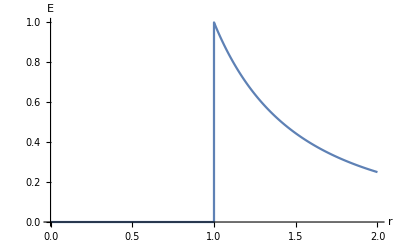

```mathematica
f1[r_]:=If[r≥1,1/r^2,0]
Plot[f1[r],{r,0,2},Exclusions->None,PlotPoints->800,Ticks->None,AxesLabel->{"r","E"}]
```

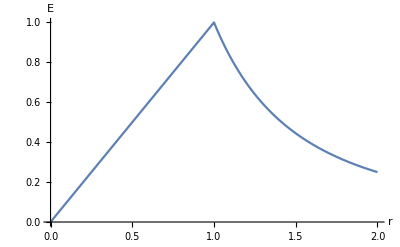

```mathematica
f2[r_]:=If[r≥1,1/r^2,r/1^3]
Plot[f2[r],{r,0,2},Exclusions->None,PlotPoints->800,Ticks->None,AxesLabel->{"r","E"}]
```

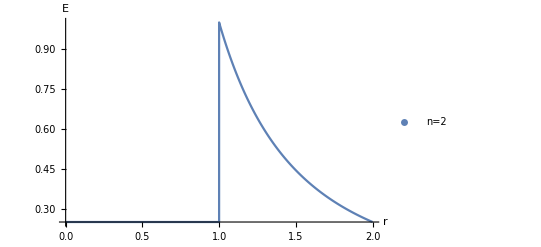

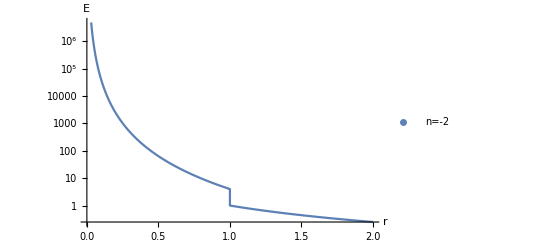

```mathematica
f3[r_,n_]:=If[r≥1,1/r^2,r^(n-2)/2^n]
Plot[f3[r,2],{r,0,2},Exclusions->None,PlotPoints->800,Ticks->None,AxesLabel->{"r","E"},PlotLegends->PointLegend[{"n=2"}]]
Plot[f3[r,-2],{r,0,2},Exclusions->None,PlotPoints->800,Ticks->None,AxesLabel->{"r","E"},ScalingFunctions->"Log",PlotLegends->PointLegend[{"n=-2"}]]
```

```mathematica
FromPolarCoordinates[{ρ,ϕ}]
ToSphericalCoordinates[{ρ Cos[ϕ],ρ Sin[ϕ],z}]
```

{ρ Cos[ϕ],ρ Sin[ϕ]}

{√(z^2+ρ^2 Cos[ϕ]^2+ρ^2 Sin[ϕ]^2),ArcTan[z,√(ρ^2 Cos[ϕ]^2+ρ^2 Sin[ϕ]^2)],ArcTan[ρ Cos[ϕ],ρ Sin[ϕ]]}

```mathematica
ToSphericalCoordinates[{ρ Cos[ϕ],ρ Sin[ϕ],z}]//Simplify
```

{√(z^2+ρ^2),ArcTan[z,√(ρ^2)],ArcTan[ρ Cos[ϕ],ρ Sin[ϕ]]}

```mathematica
FromSphericalCoordinates[{r,θ,ϕ}]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

```mathematica
ToPolarCoordinates[{x,y}]//Simplify
```

{√(x^2+y^2),ArcTan[x,y]}

```mathematica
√(x^2+y^2)/.{x-> r Cos[ϕ] Sin[θ],y-> r Sin[θ] Sin[ϕ]}//Simplify
ArcTan[x,y]/.{x-> r Cos[ϕ] Sin[θ],y-> r Sin[θ] Sin[ϕ]}//Simplify
```

√(r^2 Sin[θ]^2)

ArcTan[r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ]]

```mathematica
Manipulate[Plot[UnitStep[2-x*Sin[θ]],{x,0,6},PlotStyle->Thick],{θ,0,π}]
```

```mathematica
x+c^2
```

c^2+x

```mathematica
Manipulate[Plot[c^2+x,{x,-6.,6.}],{c,-2.2882456112707374,2.2882456112707374}]
```